# QuESTlink

QuESTlink is a symbolic and numerical simulator of quantum circuits, state-vectors, density matrices and Hamiltonians, which aims to be as usable as it is fast. It supports multithreading, GPU-acceleration and deployment to remote hardware, and a wide array of simulation, drawing and analysis facilities.

By Tyson Jones and Simon C Benjamin,
University of Oxford & Quantum Motion, UK

## Installation

Downloading, installing and configuring a quantum simulator can be a tedious overhead to jumping into research questions. We make obtaining the latest QuESTlink version a breeze:

```mathematica
Import["https://qtechtheory.org/questlink.m"];
(*CreateDownloadedQuESTEnv[];*)
```

Compiling manually from source with: OS=MACOS LIBS="-lm -lc++ /Applications/Wolfram\ Desktop\ 13.1.app/Contents/SystemFiles/Links/WSTP/DeveloperKit/MacOSX-ARM64/CompilerAdditions/libWSTPi4.a -framework Foundation" make-e

```mathematica
Install["~/src/QuESTlink/quest_link"];
```

## Demonstrations

Circuits are specified symbolically in a concise syntax faithful to the quantum computing literature.

```mathematica
?R
```

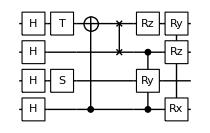

```mathematica
c = Circuit[ Subscript[H, 0] Subscript[H, 1] Subscript[H, 2] Subscript[H, 3] Subscript[S, 1] Subscript[T, 3] Subscript[C, 0][Subscript[X, 3]] Subscript[SWAP, 2,3] Subscript[C, 2,0][Subscript[Ry, 1][θ]]Subscript[Rz, 3][ϕ] R[λ,Subscript[X, 0] Subscript[Z, 2] Subscript[Y, 3]] ];
DrawCircuit[c]
```

```mathematica
<<Wolfram`QuantumFramework`
```

```mathematica
FromQuESTLink // ClearAll
FromQuESTLink[name_Symbol] := ToUpperCase @ SymbolName[name]

(* new named QuantumOperator? *)
FromQuESTLink[R[lambda_, ops_]] := Exp[- I / 2 lambda QuantumTensorProduct[FromQuESTLink[#] & /@ Flatten[Replace[{ops}, HoldPattern[Times[args___]] :> {args}, {1}]]]]

FromQuESTLink[Subscript[Depol, order__][args___]] := QuantumChannel[{"Depol", args}, {order} + 1]

FromQuESTLink[Subscript[C, order__Integer][op_]] := QuantumOperator[{"C", FromQuESTLink[op], {order} + 1}]

FromQuESTLink[Subscript[name_Symbol, order__Integer]] := QuantumOperator[FromQuESTLink[name], {order} + 1]
FromQuESTLink[Subscript[name_Symbol, order__Integer][args___]] := QuantumOperator[{FromQuESTLink[name], args}, {order} + 1]
FromQuESTLink[ops_List] := With[{width = Max[Cases[ops, Subscript[_, order__Integer] :> {order}, All]] + 1}, QuantumCircuitOperator[FromQuESTLink[#] & /@ ops]]
```

Notice different order, QuEST uses reverse convention for its diagram, counting qubits in bottom-up direction.

QuantumCircuitOperator[…]

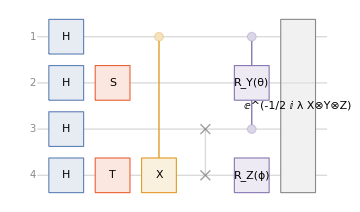

```mathematica
circuit=FromQuESTLink[c]
circuit["Diagram"]
```

They can be analytically studied

```mathematica
m = CalcCircuitMatrix[c];
m⟦1,1⟧
```

1/4 ⅇ^(-(ⅈ ϕ)/2) Cos[λ/2]-1/4 ⅇ^((ⅈ π)/4+(ⅈ ϕ)/2) Sin[λ/2]

After some massaging it’s the same:

```mathematica
circuit["Matrix"][[1,1]]//ComplexExpand//FullSimplify
%/.x_?NumericQ:>Abs[x]Exp[I Arg[x]]//Expand
```

1/4 ⅇ^(-(ⅈ ϕ)/2) (Cos[λ/2]-(-1)^(1/4) ⅇ^(ⅈ ϕ) Sin[λ/2])

1/4 ⅇ^(-(ⅈ ϕ)/2) Cos[λ/2]-1/4 ⅇ^((ⅈ π)/4+(ⅈ ϕ)/2) Sin[λ/2]

or efficiently numerically simulated in the QuEST C++ backend, which one can compile to be multithreaded, GPU-accelerated and server-side.

```mathematica
ψ = CreateQureg[4];
StartRecordingQASM[ψ];
ApplyCircuit[ψ, c /. {θ->π/3,ϕ->π/4,λ->π/5}];
GetQuregMatrix[ψ] // MatrixForm
```

(0.190101-0.162362 ⅈ
0.148292+0.0614245 ⅈ
0.162362+0.190101 ⅈ
-0.0614245+0.148292 ⅈ
0.296259+0.0809047 ⅈ
0.174306-0.117257 ⅈ
-0.0809047+0.296259 ⅈ
0.117257+0.174306 ⅈ
0.291039+0.120552 ⅈ
0.162362+0.190101 ⅈ
-0.120552+0.291039 ⅈ
-0.190101+0.162362 ⅈ
0.043959+0.280955 ⅈ
0.164356-0.0605984 ⅈ
-0.280955+0.043959 ⅈ
0.0605984+0.164356 ⅈ)

```mathematica
GetRecordedQASM[ψ]
```

OPENQASM 2.0;
qreg q[4];
creg c[4];
h q[0];
h q[1];
h q[2];
h q[3];
s q[1];
t q[3];
cx q[0],q[3];
cswap q[2],q[3];
// Here a 2-control 1-target multiControlledMultiRotatePauli of angle 1.0471975511966 was performed (QASM not yet implemented)
Rz(0.78539816339745) q[3];
// Here a 3-qubit multiRotatePauli of angle 0.62831853071796 was performed (QASM not yet implemented)

```mathematica
FromQuESTLink[c /. {θ->π/3,ϕ->π/4,λ->π/5}]["QASM"]
```

OPENQASM 3.0;
qubit[4] q;
bit[0] c;
U(pi/2, 0, pi) q[0];
U(pi/2, 0, pi) q[1];
U(pi/2, 0, pi) q[2];
U(pi/2, 0, pi) q[3];
U(0, 0, pi) q[1];
U(0, 0, pi) q[3];
ctrl(1) @ negctrl(0) @ U(pi, 0, pi) q[0] q[3];
swap q[2] q[3];
ctrl(2) @ negctrl(0) @ U(pi/3, 0, 0) q[2] q[0] q[1];
U(0, 0, pi) q[3];
// Unimplimented QASM for operator with label: Power[E, Times[0 - 0.1i, Pi, CircleTimes[X, Y, Z]]] ---- q[0] q[2] q[3];

“Reverse” because of reverse convention again.

```mathematica
Normal[circuit[]["Reverse"]["Matrix"]] /. {θ->π/3,ϕ->π/4,λ->π/5}//N//MatrixForm
```

(0.190101-0.162362 ⅈ
0.148292+0.0614245 ⅈ
0.162362+0.190101 ⅈ
-0.0614245+0.148292 ⅈ
0.296259+0.0809047 ⅈ
0.174306-0.117257 ⅈ
-0.0809047+0.296259 ⅈ
0.117257+0.174306 ⅈ
0.291039+0.120552 ⅈ
0.162362+0.190101 ⅈ
-0.120552+0.291039 ⅈ
-0.190101+0.162362 ⅈ
0.043959+0.280955 ⅈ
0.164356-0.0605984 ⅈ
-0.280955+0.043959 ⅈ
0.0605984+0.164356 ⅈ)

This allows advanced questions to be rapidly answered, such as the approximate energy extrema of our circuit with equal parameters under a funky Pauli Hamiltonian:

```mathematica
h = SimplifyPaulis[ 
	(.1 Subscript[X, 0] + .2 Subscript[Z, 0] Subscript[X, 1])^3 (.1 Subscript[X, 0] Subscript[Y, 1] - .6 Subscript[Z, 2] Subscript[Z, 3] + .5 Subscript[Y, 0] Subscript[Y, 1] Subscript[Z, 2] Subscript[X, 3])^2 + 
	.2(Subscript[X, 2] Subscript[X, 3] +  Subscript[Y, 3] Subscript[Y, 0] + Subscript[Z, 0] Subscript[Z, 1] + Subscript[X, 1] Subscript[X, 2])
] // Chop
```

-0.00186 X_0+0.2 X_1 X_2+0.2 X_2 X_3+0.2 Y_0 Y_3+0.0062 X_1 Z_0+0.2 Z_0 Z_1+0.00036 Y_1 Z_2 Z_3-0.0012 Y_0 Z_1 Z_2 Z_3

```mathematica
MakePualiOperators[h_] := List @@ h /. op : Times[c_ ? NumericQ, ops__] :> QuantumOperator[c QuantumTensorProduct[FromQuESTLink /@ {ops}], "Label" -> op]
```

```mathematica
pauliOps=MakePualiOperators[h];
```

```mathematica
pauliOp=Plus@@pauliOps
```

QuantumOperator[…]

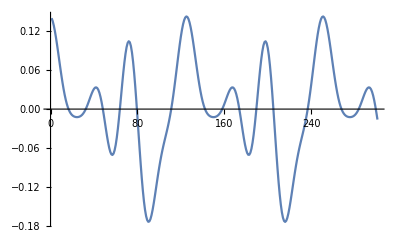

{0.142713,-0.173802}

```mathematica
tmp = CreateQureg[4];
data = Table[
	ApplyCircuit[InitZeroState[ψ], c /. {θ->v,ϕ->v,λ->v}];
	CalcExpecPauliSum[ψ, h, tmp],
	{v, 0, 30, .1}];

ListLinePlot[data]
{Max[data], Min[data]}
```

All expressions can be precomputed:

```mathematica
finalState=circuit[];
expectedPauliSum=(finalState["Dagger"]@pauliOp@finalState)["Number"];
```

```mathematica
data = Table[
	Chop[expectedPauliSum/. {θ->v,ϕ->v,λ->v}],
	{v, 0, 30, .1}];

ListLinePlot[data]
{Max[data], Min[data]}
```

-Graphics-

{0.142713,-0.173802}

### Suzuki-Trotter simulation

Many quantum algorithms become trivial and concise to express. Here are all orders of the Suzuki-Trotter decomposition of a Hamiltonian h!

```mathematica
symmetrize[h_, λ_, 1] := λ h
symmetrize[h_, λ_, 2] := With[
	{s1 = symmetrize[h, λ/2, 1]}, 
	Join[s1,Reverse[s1]]]
symmetrize[h_, λ_, n_?EvenQ] := Block[
	{γ, p=1/(4-4^(1/(n-1)))}, With[
       {s=symmetrize[h,γ,n-2]}, With[
     {r=s /. γ -> λ p},
	     Join[r, r, s /. γ -> (1-4p)λ, r, r]]]]

gateify[Verbatim[Times][θ_, σ__]] := 
	R[2 θ, Times[σ]]
trotterize[h_, n_, r_, t_] :=With[
	{s=symmetrize[List @@ h, t/r, n]},
	 gateify /@ Flatten @ ConstantArray[s, r]]
```

```mathematica
QuantumCircuitOperator[{"Trotterization",MakePualiOperators[h],2,1,.1}][]==FromQuESTLink[trotterize[h, 2, 1, .1]][]
```

True

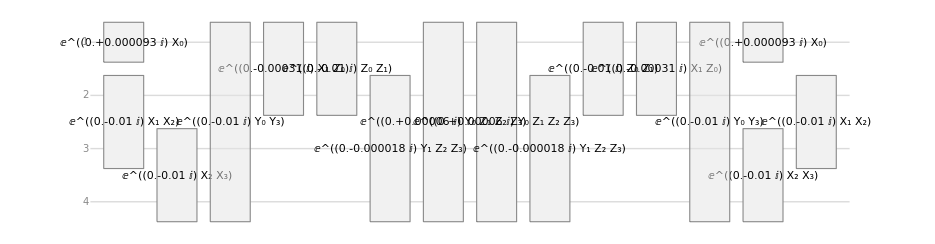

```mathematica
QuantumCircuitOperator[{"Trotterization",MakePualiOperators[h],2,1,.1}]["Diagram"]
```

We have many ways to rapidly visualise these circuits.

BCH approximation

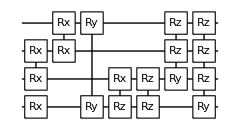

```mathematica
DrawCircuit @ trotterize[h, 1, 1, .1]
```

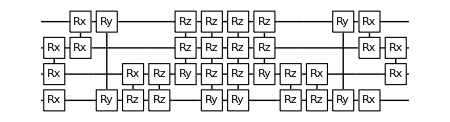

```mathematica
DrawCircuit @ trotterize[h, 2, 1, .1]
```

```mathematica
CalcCircuitMatrix @  trotterize[h, 1, 1, 1] // MatrixForm
```

(0.922598-0.187016 ⅈ | 0.00140676+0.00195288 ⅈ | -0.00147926-0.00578119 ⅈ | -0.00154883-0.00768074 ⅈ | -0.00120439+0.000363672 ⅈ | 0.0379117-0.00768673 ⅈ | -0.0379095-0.18702 ⅈ | 0.000332056-0.000532754 ⅈ | -0.00024107+0.0000839063 ⅈ | 0.0379105+0.18702 ⅈ | -0.0379088+0.00768728 ⅈ | 0.0011134-0.000382111 ⅈ | -0.0379095-0.18702 ⅈ | 0.000332056-0.000532754 ⅈ | -0.00120439+0.000363672 ⅈ | 0.0379117-0.00768673 ⅈ
-0.00150318+0.00192803 ⅈ | 0.922598+0.187016 ⅈ | -0.00156678+0.00768908 ⅈ | -0.00150411+0.00579384 ⅈ | -0.03791-0.00768309 ⅈ | 0.00114199+0.000241088 ⅈ | 0.000454644+0.0000571209 ⅈ | 0.0379105-0.187019 ⅈ | 0.0379112-0.18702 ⅈ | 0.00036366-0.000391727 ⅈ | 0.00123297+0.000222639 ⅈ | -0.0379128-0.00768219 ⅈ | 0.000454644+0.0000571209 ⅈ | 0.0379105-0.187019 ⅈ | -0.03791-0.00768309 ⅈ | 0.00114199+0.000241088 ⅈ
0.00150411-0.00579384 ⅈ | 0.00156678-0.00768908 ⅈ | 0.922598+0.187016 ⅈ | -0.00150318+0.00192803 ⅈ | 0.0379105-0.187019 ⅈ | 0.000454644+0.0000571209 ⅈ | -0.00114199-0.000241088 ⅈ | 0.03791+0.00768309 ⅈ | -0.0379128-0.00768219 ⅈ | 0.00123297+0.000222639 ⅈ | -0.00036366+0.000391727 ⅈ | -0.0379112+0.18702 ⅈ | -0.00114199-0.000241088 ⅈ | 0.03791+0.00768309 ⅈ | 0.0379105-0.187019 ⅈ | 0.000454644+0.0000571209 ⅈ
0.00154883+0.00768074 ⅈ | 0.00147926+0.00578119 ⅈ | 0.00140676+0.00195288 ⅈ | 0.922598-0.187016 ⅈ | 0.000332056-0.000532754 ⅈ | -0.0379095-0.18702 ⅈ | -0.0379117+0.00768673 ⅈ | 0.00120439-0.000363672 ⅈ | 0.0011134-0.000382111 ⅈ | -0.0379088+0.00768728 ⅈ | -0.0379105-0.18702 ⅈ | 0.00024107-0.0000839063 ⅈ | -0.0379117+0.00768673 ⅈ | 0.00120439-0.000363672 ⅈ | 0.000332056-0.000532754 ⅈ | -0.0379095-0.18702 ⅈ
-0.0010861+0.000247457 ⅈ | 0.0379092-0.00768724 ⅈ | -0.0379113-0.18702 ⅈ | 0.000268365-0.0000783745 ⅈ | 0.9226-0.187024 ⅈ | -0.000806344+0.0014985 ⅈ | -0.000811228-0.00566498 ⅈ | -0.0015463-0.00769323 ⅈ | -0.0379113-0.18702 ⅈ | 0.000268365-0.0000783745 ⅈ | -0.0010861+0.000247457 ⅈ | 0.0379092-0.00768724 ⅈ | -0.000359353+0.000527223 ⅈ | 0.0379104+0.18702 ⅈ | -0.0379119+0.00768701 ⅈ | 0.00117709-0.000229018 ⅈ
-0.0379125-0.00768257 ⅈ | 0.00120568+0.0000879842 ⅈ | 0.000336364-0.000386193 ⅈ | 0.0379121-0.18702 ⅈ | 0.000712172+0.00148472 ⅈ | 0.9226+0.187024 ⅈ | -0.00156932+0.00767658 ⅈ | -0.000843554+0.00564074 ⅈ | 0.000336364-0.000386193 ⅈ | 0.0379121-0.18702 ⅈ | -0.0379125-0.00768257 ⅈ | 0.00120568+0.0000879842 ⅈ | 0.0379113-0.18702 ⅈ | 0.00042735+0.0000626557 ⅈ | 0.00111469+0.000106433 ⅈ | -0.0379098-0.00768315 ⅈ
0.0379121-0.18702 ⅈ | 0.000336364-0.000386193 ⅈ | -0.00120568-0.0000879842 ⅈ | 0.0379125+0.00768257 ⅈ | 0.000843554-0.00564074 ⅈ | 0.00156932-0.00767658 ⅈ | 0.9226+0.187024 ⅈ | 0.000712172+0.00148472 ⅈ | -0.00120568-0.0000879842 ⅈ | 0.0379125+0.00768257 ⅈ | 0.0379121-0.18702 ⅈ | 0.000336364-0.000386193 ⅈ | -0.0379098-0.00768315 ⅈ | 0.00111469+0.000106433 ⅈ | -0.00042735-0.0000626557 ⅈ | -0.0379113+0.18702 ⅈ
0.000268365-0.0000783745 ⅈ | -0.0379113-0.18702 ⅈ | -0.0379092+0.00768724 ⅈ | 0.0010861-0.000247457 ⅈ | 0.0015463+0.00769323 ⅈ | 0.000811228+0.00566498 ⅈ | -0.000806344+0.0014985 ⅈ | 0.9226-0.187024 ⅈ | -0.0379092+0.00768724 ⅈ | 0.0010861-0.000247457 ⅈ | 0.000268365-0.0000783745 ⅈ | -0.0379113-0.18702 ⅈ | 0.00117709-0.000229018 ⅈ | -0.0379119+0.00768701 ⅈ | -0.0379104-0.18702 ⅈ | 0.000359353-0.000527223 ⅈ
0.00042735-0.0000626557 ⅈ | -0.0379113-0.18702 ⅈ | -0.0379098+0.00768315 ⅈ | -0.00111469+0.000106433 ⅈ | -0.0379121-0.18702 ⅈ | 0.000336364+0.000386193 ⅈ | -0.00120568+0.0000879842 ⅈ | -0.0379125+0.00768257 ⅈ | 0.9226-0.187024 ⅈ | -0.000712172+0.00148472 ⅈ | -0.000843554-0.00564074 ⅈ | 0.00156932+0.00767658 ⅈ | -0.00120568+0.0000879842 ⅈ | -0.0379125+0.00768257 ⅈ | -0.0379121-0.18702 ⅈ | 0.000336364+0.000386193 ⅈ
-0.0379104+0.18702 ⅈ | -0.000359353-0.000527223 ⅈ | -0.00117709-0.000229018 ⅈ | -0.0379119-0.00768701 ⅈ | 0.000268365+0.0000783745 ⅈ | 0.0379113-0.18702 ⅈ | 0.0379092+0.00768724 ⅈ | 0.0010861+0.000247457 ⅈ | 0.000806344+0.0014985 ⅈ | 0.9226+0.187024 ⅈ | 0.0015463-0.00769323 ⅈ | -0.000811228+0.00566498 ⅈ | 0.0379092+0.00768724 ⅈ | 0.0010861+0.000247457 ⅈ | 0.000268365+0.0000783745 ⅈ | 0.0379113-0.18702 ⅈ
-0.0379119-0.00768701 ⅈ | -0.00117709-0.000229018 ⅈ | 0.000359353+0.000527223 ⅈ | 0.0379104-0.18702 ⅈ | -0.0010861-0.000247457 ⅈ | -0.0379092-0.00768724 ⅈ | 0.0379113-0.18702 ⅈ | 0.000268365+0.0000783745 ⅈ | 0.000811228-0.00566498 ⅈ | -0.0015463+0.00769323 ⅈ | 0.9226+0.187024 ⅈ | 0.000806344+0.0014985 ⅈ | 0.0379113-0.18702 ⅈ | 0.000268365+0.0000783745 ⅈ | -0.0010861-0.000247457 ⅈ | -0.0379092-0.00768724 ⅈ
-0.00111469+0.000106433 ⅈ | -0.0379098+0.00768315 ⅈ | 0.0379113+0.18702 ⅈ | -0.00042735+0.0000626557 ⅈ | 0.0379125-0.00768257 ⅈ | 0.00120568-0.0000879842 ⅈ | 0.000336364+0.000386193 ⅈ | -0.0379121-0.18702 ⅈ | -0.00156932-0.00767658 ⅈ | 0.000843554+0.00564074 ⅈ | -0.000712172+0.00148472 ⅈ | 0.9226-0.187024 ⅈ | 0.000336364+0.000386193 ⅈ | -0.0379121-0.18702 ⅈ | 0.0379125-0.00768257 ⅈ | 0.00120568-0.0000879842 ⅈ
-0.0379105-0.187019 ⅈ | 0.000454644-0.0000571209 ⅈ | -0.00114199+0.000241088 ⅈ | -0.03791+0.00768309 ⅈ | 0.00036366+0.000391727 ⅈ | -0.0379112-0.18702 ⅈ | -0.0379128+0.00768219 ⅈ | -0.00123297+0.000222639 ⅈ | -0.00114199+0.000241088 ⅈ | -0.03791+0.00768309 ⅈ | -0.0379105-0.187019 ⅈ | 0.000454644-0.0000571209 ⅈ | 0.922598-0.187016 ⅈ | 0.00150318+0.00192803 ⅈ | -0.00150411-0.00579384 ⅈ | 0.00156678+0.00768908 ⅈ
0.000332056+0.000532754 ⅈ | 0.0379095-0.18702 ⅈ | 0.0379117+0.00768673 ⅈ | 0.00120439+0.000363672 ⅈ | -0.0379105+0.18702 ⅈ | -0.00024107-0.0000839063 ⅈ | -0.0011134-0.000382111 ⅈ | -0.0379088-0.00768728 ⅈ | 0.0379117+0.00768673 ⅈ | 0.00120439+0.000363672 ⅈ | 0.000332056+0.000532754 ⅈ | 0.0379095-0.18702 ⅈ | -0.00140676+0.00195288 ⅈ | 0.922598+0.187016 ⅈ | 0.00154883-0.00768074 ⅈ | -0.00147926+0.00578119 ⅈ
-0.00120439-0.000363672 ⅈ | -0.0379117-0.00768673 ⅈ | 0.0379095-0.18702 ⅈ | 0.000332056+0.000532754 ⅈ | -0.0379088-0.00768728 ⅈ | -0.0011134-0.000382111 ⅈ | 0.00024107+0.0000839063 ⅈ | 0.0379105-0.18702 ⅈ | 0.0379095-0.18702 ⅈ | 0.000332056+0.000532754 ⅈ | -0.00120439-0.000363672 ⅈ | -0.0379117-0.00768673 ⅈ | 0.00147926-0.00578119 ⅈ | -0.00154883+0.00768074 ⅈ | 0.922598+0.187016 ⅈ | -0.00140676+0.00195288 ⅈ
0.03791-0.00768309 ⅈ | 0.00114199-0.000241088 ⅈ | 0.000454644-0.0000571209 ⅈ | -0.0379105-0.187019 ⅈ | -0.00123297+0.000222639 ⅈ | -0.0379128+0.00768219 ⅈ | 0.0379112+0.18702 ⅈ | -0.00036366-0.000391727 ⅈ | 0.000454644-0.0000571209 ⅈ | -0.0379105-0.187019 ⅈ | 0.03791-0.00768309 ⅈ | 0.00114199-0.000241088 ⅈ | -0.00156678-0.00768908 ⅈ | 0.00150411+0.00579384 ⅈ | 0.00150318+0.00192803 ⅈ | 0.922598-0.187016 ⅈ)

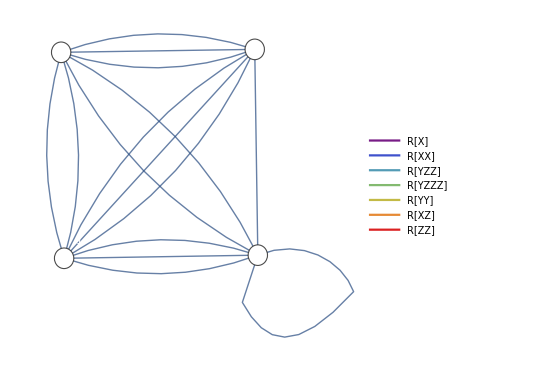

```mathematica
DrawCircuitTopology @ trotterize[h, 2, 1, .1]
```

```mathematica
QuantumCircuitOperator[{"Trotterization",MakePualiOperators[h],1,1,1}]["Reverse"]["Matrix"]// MatrixForm
```

(0.922598-0.187016 ⅈ | 0.00140676+0.00195288 ⅈ | -0.00147926-0.00578119 ⅈ | -0.00154883-0.00768074 ⅈ | -0.00120439+0.000363672 ⅈ | 0.0379117-0.00768673 ⅈ | -0.0379095-0.18702 ⅈ | 0.000332056-0.000532754 ⅈ | -0.00024107+0.0000839063 ⅈ | 0.0379105+0.18702 ⅈ | -0.0379088+0.00768728 ⅈ | 0.0011134-0.000382111 ⅈ | -0.0379095-0.18702 ⅈ | 0.000332056-0.000532754 ⅈ | -0.00120439+0.000363672 ⅈ | 0.0379117-0.00768673 ⅈ
-0.00150318+0.00192803 ⅈ | 0.922598+0.187016 ⅈ | -0.00156678+0.00768908 ⅈ | -0.00150411+0.00579384 ⅈ | -0.03791-0.00768309 ⅈ | 0.00114199+0.000241088 ⅈ | 0.000454644+0.0000571209 ⅈ | 0.0379105-0.187019 ⅈ | 0.0379112-0.18702 ⅈ | 0.00036366-0.000391727 ⅈ | 0.00123297+0.000222639 ⅈ | -0.0379128-0.00768219 ⅈ | 0.000454644+0.0000571209 ⅈ | 0.0379105-0.187019 ⅈ | -0.03791-0.00768309 ⅈ | 0.00114199+0.000241088 ⅈ
0.00150411-0.00579384 ⅈ | 0.00156678-0.00768908 ⅈ | 0.922598+0.187016 ⅈ | -0.00150318+0.00192803 ⅈ | 0.0379105-0.187019 ⅈ | 0.000454644+0.0000571209 ⅈ | -0.00114199-0.000241088 ⅈ | 0.03791+0.00768309 ⅈ | -0.0379128-0.00768219 ⅈ | 0.00123297+0.000222639 ⅈ | -0.00036366+0.000391727 ⅈ | -0.0379112+0.18702 ⅈ | -0.00114199-0.000241088 ⅈ | 0.03791+0.00768309 ⅈ | 0.0379105-0.187019 ⅈ | 0.000454644+0.0000571209 ⅈ
0.00154883+0.00768074 ⅈ | 0.00147926+0.00578119 ⅈ | 0.00140676+0.00195288 ⅈ | 0.922598-0.187016 ⅈ | 0.000332056-0.000532754 ⅈ | -0.0379095-0.18702 ⅈ | -0.0379117+0.00768673 ⅈ | 0.00120439-0.000363672 ⅈ | 0.0011134-0.000382111 ⅈ | -0.0379088+0.00768728 ⅈ | -0.0379105-0.18702 ⅈ | 0.00024107-0.0000839063 ⅈ | -0.0379117+0.00768673 ⅈ | 0.00120439-0.000363672 ⅈ | 0.000332056-0.000532754 ⅈ | -0.0379095-0.18702 ⅈ
-0.0010861+0.000247457 ⅈ | 0.0379092-0.00768724 ⅈ | -0.0379113-0.18702 ⅈ | 0.000268365-0.0000783745 ⅈ | 0.9226-0.187024 ⅈ | -0.000806344+0.0014985 ⅈ | -0.000811228-0.00566498 ⅈ | -0.0015463-0.00769323 ⅈ | -0.0379113-0.18702 ⅈ | 0.000268365-0.0000783745 ⅈ | -0.0010861+0.000247457 ⅈ | 0.0379092-0.00768724 ⅈ | -0.000359353+0.000527223 ⅈ | 0.0379104+0.18702 ⅈ | -0.0379119+0.00768701 ⅈ | 0.00117709-0.000229018 ⅈ
-0.0379125-0.00768257 ⅈ | 0.00120568+0.0000879842 ⅈ | 0.000336364-0.000386193 ⅈ | 0.0379121-0.18702 ⅈ | 0.000712172+0.00148472 ⅈ | 0.9226+0.187024 ⅈ | -0.00156932+0.00767658 ⅈ | -0.000843554+0.00564074 ⅈ | 0.000336364-0.000386193 ⅈ | 0.0379121-0.18702 ⅈ | -0.0379125-0.00768257 ⅈ | 0.00120568+0.0000879842 ⅈ | 0.0379113-0.18702 ⅈ | 0.00042735+0.0000626557 ⅈ | 0.00111469+0.000106433 ⅈ | -0.0379098-0.00768315 ⅈ
0.0379121-0.18702 ⅈ | 0.000336364-0.000386193 ⅈ | -0.00120568-0.0000879842 ⅈ | 0.0379125+0.00768257 ⅈ | 0.000843554-0.00564074 ⅈ | 0.00156932-0.00767658 ⅈ | 0.9226+0.187024 ⅈ | 0.000712172+0.00148472 ⅈ | -0.00120568-0.0000879842 ⅈ | 0.0379125+0.00768257 ⅈ | 0.0379121-0.18702 ⅈ | 0.000336364-0.000386193 ⅈ | -0.0379098-0.00768315 ⅈ | 0.00111469+0.000106433 ⅈ | -0.00042735-0.0000626557 ⅈ | -0.0379113+0.18702 ⅈ
0.000268365-0.0000783745 ⅈ | -0.0379113-0.18702 ⅈ | -0.0379092+0.00768724 ⅈ | 0.0010861-0.000247457 ⅈ | 0.0015463+0.00769323 ⅈ | 0.000811228+0.00566498 ⅈ | -0.000806344+0.0014985 ⅈ | 0.9226-0.187024 ⅈ | -0.0379092+0.00768724 ⅈ | 0.0010861-0.000247457 ⅈ | 0.000268365-0.0000783745 ⅈ | -0.0379113-0.18702 ⅈ | 0.00117709-0.000229018 ⅈ | -0.0379119+0.00768701 ⅈ | -0.0379104-0.18702 ⅈ | 0.000359353-0.000527223 ⅈ
0.00042735-0.0000626557 ⅈ | -0.0379113-0.18702 ⅈ | -0.0379098+0.00768315 ⅈ | -0.00111469+0.000106433 ⅈ | -0.0379121-0.18702 ⅈ | 0.000336364+0.000386193 ⅈ | -0.00120568+0.0000879842 ⅈ | -0.0379125+0.00768257 ⅈ | 0.9226-0.187024 ⅈ | -0.000712172+0.00148472 ⅈ | -0.000843554-0.00564074 ⅈ | 0.00156932+0.00767658 ⅈ | -0.00120568+0.0000879842 ⅈ | -0.0379125+0.00768257 ⅈ | -0.0379121-0.18702 ⅈ | 0.000336364+0.000386193 ⅈ
-0.0379104+0.18702 ⅈ | -0.000359353-0.000527223 ⅈ | -0.00117709-0.000229018 ⅈ | -0.0379119-0.00768701 ⅈ | 0.000268365+0.0000783745 ⅈ | 0.0379113-0.18702 ⅈ | 0.0379092+0.00768724 ⅈ | 0.0010861+0.000247457 ⅈ | 0.000806344+0.0014985 ⅈ | 0.9226+0.187024 ⅈ | 0.0015463-0.00769323 ⅈ | -0.000811228+0.00566498 ⅈ | 0.0379092+0.00768724 ⅈ | 0.0010861+0.000247457 ⅈ | 0.000268365+0.0000783745 ⅈ | 0.0379113-0.18702 ⅈ
-0.0379119-0.00768701 ⅈ | -0.00117709-0.000229018 ⅈ | 0.000359353+0.000527223 ⅈ | 0.0379104-0.18702 ⅈ | -0.0010861-0.000247457 ⅈ | -0.0379092-0.00768724 ⅈ | 0.0379113-0.18702 ⅈ | 0.000268365+0.0000783745 ⅈ | 0.000811228-0.00566498 ⅈ | -0.0015463+0.00769323 ⅈ | 0.9226+0.187024 ⅈ | 0.000806344+0.0014985 ⅈ | 0.0379113-0.18702 ⅈ | 0.000268365+0.0000783745 ⅈ | -0.0010861-0.000247457 ⅈ | -0.0379092-0.00768724 ⅈ
-0.00111469+0.000106433 ⅈ | -0.0379098+0.00768315 ⅈ | 0.0379113+0.18702 ⅈ | -0.00042735+0.0000626557 ⅈ | 0.0379125-0.00768257 ⅈ | 0.00120568-0.0000879842 ⅈ | 0.000336364+0.000386193 ⅈ | -0.0379121-0.18702 ⅈ | -0.00156932-0.00767658 ⅈ | 0.000843554+0.00564074 ⅈ | -0.000712172+0.00148472 ⅈ | 0.9226-0.187024 ⅈ | 0.000336364+0.000386193 ⅈ | -0.0379121-0.18702 ⅈ | 0.0379125-0.00768257 ⅈ | 0.00120568-0.0000879842 ⅈ
-0.0379105-0.187019 ⅈ | 0.000454644-0.0000571209 ⅈ | -0.00114199+0.000241088 ⅈ | -0.03791+0.00768309 ⅈ | 0.00036366+0.000391727 ⅈ | -0.0379112-0.18702 ⅈ | -0.0379128+0.00768219 ⅈ | -0.00123297+0.000222639 ⅈ | -0.00114199+0.000241088 ⅈ | -0.03791+0.00768309 ⅈ | -0.0379105-0.187019 ⅈ | 0.000454644-0.0000571209 ⅈ | 0.922598-0.187016 ⅈ | 0.00150318+0.00192803 ⅈ | -0.00150411-0.00579384 ⅈ | 0.00156678+0.00768908 ⅈ
0.000332056+0.000532754 ⅈ | 0.0379095-0.18702 ⅈ | 0.0379117+0.00768673 ⅈ | 0.00120439+0.000363672 ⅈ | -0.0379105+0.18702 ⅈ | -0.00024107-0.0000839063 ⅈ | -0.0011134-0.000382111 ⅈ | -0.0379088-0.00768728 ⅈ | 0.0379117+0.00768673 ⅈ | 0.00120439+0.000363672 ⅈ | 0.000332056+0.000532754 ⅈ | 0.0379095-0.18702 ⅈ | -0.00140676+0.00195288 ⅈ | 0.922598+0.187016 ⅈ | 0.00154883-0.00768074 ⅈ | -0.00147926+0.00578119 ⅈ
-0.00120439-0.000363672 ⅈ | -0.0379117-0.00768673 ⅈ | 0.0379095-0.18702 ⅈ | 0.000332056+0.000532754 ⅈ | -0.0379088-0.00768728 ⅈ | -0.0011134-0.000382111 ⅈ | 0.00024107+0.0000839063 ⅈ | 0.0379105-0.18702 ⅈ | 0.0379095-0.18702 ⅈ | 0.000332056+0.000532754 ⅈ | -0.00120439-0.000363672 ⅈ | -0.0379117-0.00768673 ⅈ | 0.00147926-0.00578119 ⅈ | -0.00154883+0.00768074 ⅈ | 0.922598+0.187016 ⅈ | -0.00140676+0.00195288 ⅈ
0.03791-0.00768309 ⅈ | 0.00114199-0.000241088 ⅈ | 0.000454644-0.0000571209 ⅈ | -0.0379105-0.187019 ⅈ | -0.00123297+0.000222639 ⅈ | -0.0379128+0.00768219 ⅈ | 0.0379112+0.18702 ⅈ | -0.00036366-0.000391727 ⅈ | 0.000454644-0.0000571209 ⅈ | -0.0379105-0.187019 ⅈ | 0.03791-0.00768309 ⅈ | 0.00114199-0.000241088 ⅈ | -0.00156678-0.00768908 ⅈ | 0.00150411+0.00579384 ⅈ | 0.00150318+0.00192803 ⅈ | 0.922598-0.187016 ⅈ)

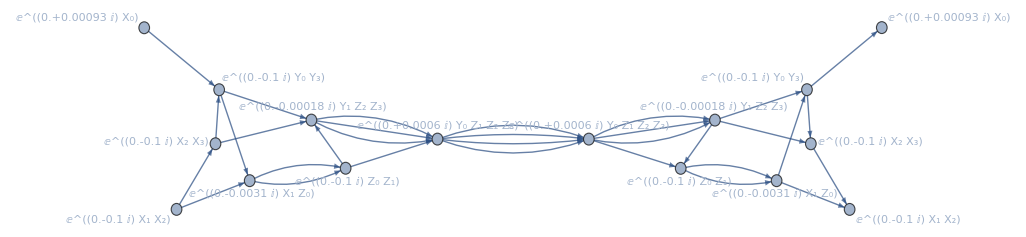

```mathematica
VertexDelete[QuantumCircuitOperator[{"Trotterization",MakePualiOperators[h],2,1,1}]["TensorNetwork"],0]
```

Topology is computed from InputOrders of operators:

```mathematica
CircuitTopology[circuit_QuantumCircuitOperator] := Block[{g, labels, colorMap},
	g = Graph[
		DeleteDuplicates @ Catenate @ MapThread[{label, order} |->
			UndirectedEdge @@ Append[Sort[#], label] & /@ If[Length[order] > 1, Subsets, Tuples][order, {2}],
			{Replace[#["Label"], HoldPattern[Power[E, Times[c_ ? NumericQ, paulis__]]] :> "R"[paulis]] & /@ circuit["Operators"], circuit["InputOrders"]}
		],
		VertexLabels -> Automatic,
		GraphLayout -> "SpringElectricalEmbedding"
	];
	labels = DeleteDuplicates[EdgeTags[g]];
	colorMap = Association @ MapIndexed[#1 -> ColorData[93][#2[[1]]] &, labels];
	Legended[Graph[g, EdgeStyle -> UndirectedEdge[_, _, label_] :> colorMap[label]], SwatchLegend[Values[colorMap], Keys[colorMap]]]
]
```

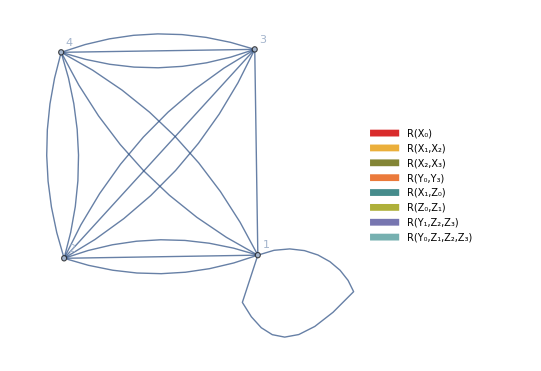

```mathematica
CircuitTopology[QuantumCircuitOperator[{"Trotterization",MakePualiOperators[h],2,1,.1}]]
```

Let’s initialise a new qureg ψtrue to a future state prescribed directly by the Schrodinger equation

```mathematica
t = 10;
ψtrue = CreateQureg[4];
SetQuregMatrix[ψtrue,
	NDSolveValue[
	{ⅈ Ψ'[τ] == CalcPauliSumMatrix[h] . Ψ[τ],
	Ψ[0] ==GetQuregMatrix @ InitZeroState[ψ]},
		Ψ, {τ,0,t}][t]];
```

and compare it to the states produced by our Trotter circuits

```mathematica
DrawCircuit@trotterize[h, 1, 20, t]
```

```mathematica
orders =  {1,2,4,6};
infids = Table[
	c =  trotterize[h, order, reps, t];
	ApplyCircuit[InitZeroState[ψ],c];
	{Length[c], 1 - CalcFidelity[ψ,ψtrue]},
	{order,orders},
	{reps, 1, 20}];
```

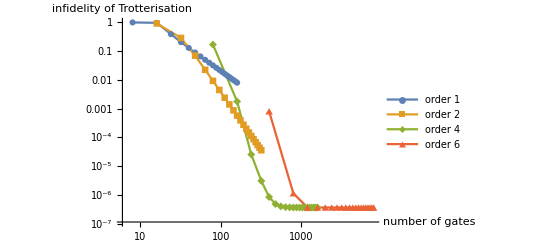

```mathematica
opts = {Joined->True,PlotMarkers->Automatic, PlotRange->Automatic,
	PlotLegends-> Table[Row[{"order ",i}], {i,orders}],
	AxesLabel-> {"number of gates", "infidelity of Trotterisation"}};

ListLogLogPlot[infids,  opts]
```

```mathematica
psiTrue=QuantumOperator[pauliOp,"ParameterSpec"->τ]["EvolutionOperator"][t][]
```

QuantumState[…]

```mathematica
infids=Monitor[Table[With[{c=QuantumCircuitOperator[{"Trotterization",pauliOps,order,reps,t}]},{c["Gates"],1-QuantumDistance[c[Method->"Schrodinger"],psiTrue,"Fidelity"]}],{order,{1,2}},{reps, 1, 20}],{order,reps}];
```

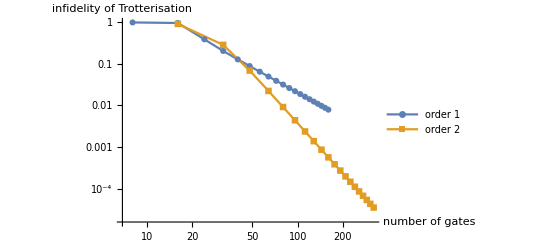

```mathematica
ListLogLogPlot[infids,opts]
```

### Noisy simulation

Since we can modify our circuits symbolically, injecting noise into our circuits is easy!

```mathematica
noisify[p_][u_] := u /. {
g:R[_, Subscript[_, qb_]]:>Sequence[g,Subscript[Depol, qb][p]], 
g:R[_, Verbatim[Times][Subscript[_, qb1_],Subscript[_, qb2_]]]:>
	Sequence[g,Subscript[Depol, qb1,qb2][p]]}
```

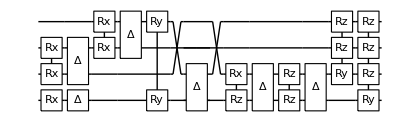

```mathematica
DrawCircuit @  noisify[10^-4] @ 
	trotterize[h,1,1,1]
```

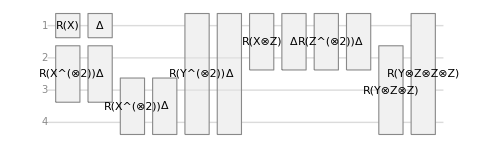

```mathematica
FromQuESTLink[noisify[10^-4]@trotterize[h,1,1,1]]["Diagram","GateLabels"->{Power[E,Verbatim[Times][_,args___]]:>"R"[args],"Depolarizing"[_]:>"Δ"}]
```

We can numerically simulate these noisy circuits using density matrices.

```mathematica
FromQuESTLink[noisify[10^-4]@trotterize[h,1,1,1]][Method->"Schrodinger"]
```

QuantumState[…]

```mathematica
ρ = CreateDensityQureg[4];
noisyInfids = Table[
	c =  noisify[10^-4] @ trotterize[h, order, reps, t];
	ApplyCircuit[InitZeroState[ρ],c];
	{Length[c], 1 - CalcFidelity[ρ,ψtrue]},
	{order,orders},
	{reps, 1, 20}];
```

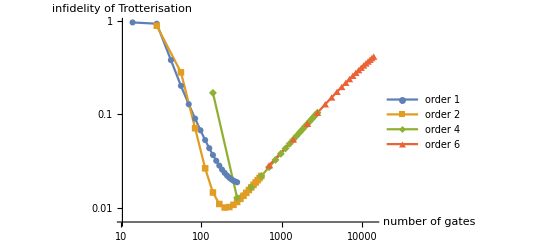

```mathematica
ListLogLogPlot[noisyInfids, opts]
```

Depolarizing channel test:

```mathematica
c1={Subscript[Depol, 0][1/9]};
ρ1= CreateDensityQureg[1];
ApplyCircuit[InitZeroState[ρ1],c1];
GetQuregMatrix[ρ1]//Chop//MatrixForm
```

(0.925926 | 0
0 | 0.0740741)

```mathematica
QuantumChannel[{"Depol",1/9}][]["DensityMatrix"]//N//MatrixForm
```

(0.925926 | 0.
0. | 0.0740741)

```mathematica
c1={Subscript[Depol, 0,1][1/9]};
ρ1= CreateDensityQureg[2];
ApplyCircuit[InitZeroState[ρ1],c1];
GetQuregMatrix[ρ1]//Chop//MatrixForm
```

(0.911111 | 0 | 0 | 0
0 | 0.0296296 | 0 | 0
0 | 0 | 0.0296296 | 0
0 | 0 | 0 | 0.0296296)

```mathematica
QuantumChannel[{"Depol",1/9},{1,2}][]["DensityMatrix"]//N//MatrixForm
```

(0.857339 | 0. | 0. | 0.
0. | 0.0685871 | 0. | 0.
0. | 0. | 0.0685871 | 0.
0. | 0. | 0. | 0.00548697)

This is what is defined in QuEST:

```mathematica
Subscript[Depol,q_][p_]:>Subscript[Kraus,q][{Sqrt[1-p] PauliMatrix[0],Sqrt[p/3] PauliMatrix[1],Sqrt[p/3] PauliMatrix[2],Sqrt[p/3] PauliMatrix[3]}],
```

```mathematica
Subscript[Depol,q1_,q2_][p_]:>Subscript[Kraus,q1,q2][Join[{Sqrt[1-p] IdentityMatrix[4]},Flatten[Table[(*the PauliMatrix[0] Kraus operator is duplicated,insignificantly*)If[n1===0&&n2===0,Nothing,Sqrt[p/15] KroneckerProduct[PauliMatrix[n1],PauliMatrix[n2]]],{n1,{0,1,2,3}},{n2,{0,1,2,3}}],1]]],
```

Coefficients are weird...

Here is that noisiest order-6 Trotter state:

```mathematica
PlotDensityMatrix[ρ]
```

-Graphics3D-

## Hungry for more?

QuESTlink has many more features not demonstrated here, including:
	• hardware accelerated numerical state analysis
	•  ansatz differentiation for simulating variational circuits
	• compilation of circuits into hardware-specific channels and circuits
	• QASM generation
	
Learn more at questlink.qtechtheory.org, or by reading the whitepaper.

```mathematica
?QuEST`*
```

GetRecordedQASM[qureg] returns the QASM recorded on qureg as a string.

```mathematica
?QuEST`Gate`*
```

```mathematica
?QuEST`Option`*
```

```mathematica
?QuEST`DeviceSpec`*
```